## Bohr and Wheeler’s Model of Fission

## The 1939 Paper

By 1939, fission had become experimentally established. However, a theoretical model of what was happening to the nucleus was lacking. Neils Bohr and John A. Wheeler, did the simplest model they could come up with. They modeled the nucleus as a charged droplet, paying no attention to quantum mechanics, or what the drop was made of, except that it had a certain amount of charge and a certain volume. Here is their abstract:

-Graphics-

Full PDF: https://www.pugetsound.edu/sites/default/files/file/7579_Bohr%20liquid%20drop_0.pdf

Amazingly, despite the fact that people were realizing that fission was potentially a weapon, this paper was published openly on September 1, 1939, at the same time as Hitler invaded Poland. Slightly less than five years later on July 16, 1944, the first fission explosion called Trinity was done at Alamogordo, NM. For more information, consult https://www.afnwc.af.mil/About-Us/History/Trinity-Nuclear-Test/.

## Legendre Polynomials

In Fig. 2, Bohr and Wheeler show how adding small contributions of these modes leads to different nuclear shapes, from nearly spherical to necked (on the verge of fission). The figure makes this progression visual: small oscillations → necking → binary division. To illustrate the question of what’s happening in between these states, we have to ask what is the mathematical model.

-Graphics-
In Fig.2, the shape deformations Wheeler and Bohr use are described with Legendre polynomials. The formula is below, however, we’re not going to go into detail just yet. Instead, we’re going to first focus on P_n which represents a Legendre of degree n before talking about the formula. 
	
	 r(θ) = R[1 + ∑α_n P_n(cosθ)]

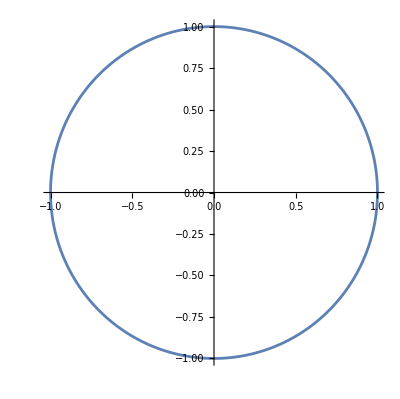
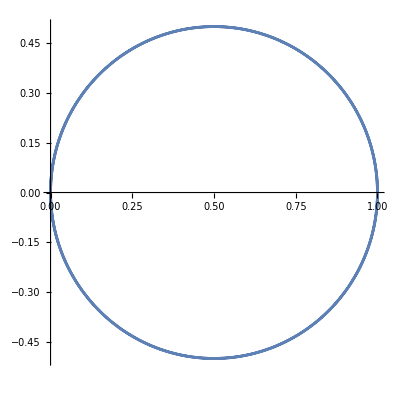
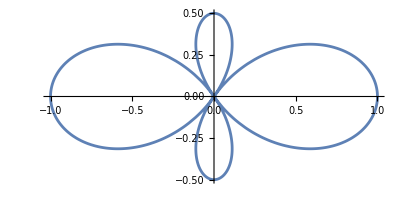
{-Graphics-P₀(cos θ),-Graphics-P₁(cos θ),-Graphics-P₂(cos θ)}

```mathematica
{Labeled[PolarPlot[LegendreP[0,Cos[θ]],{θ,0,2 π}],"P₀(cos θ)",Top],
Labeled[PolarPlot[LegendreP[1,Cos[θ]],{θ,0,2 π}],"P₁(cos θ)",Top],
Labeled[PolarPlot[LegendreP[2,Cos[θ]],{θ,0,2 π}],"P₂(cos θ)",Top]}
```

Legendre polynomials are great at describing smooth, symmetric shapes—like spheres and small deformations of spheres. In general, these polynomials show up whenever you’re dealing with problems that have spherical symmetry, like gravitational fields, electric potentials, and in this case, nuclear shapes. In the liquid drop model, we use them to describe how a nucleus deviates from a perfect sphere as it starts to deform. Each polynomial, labeled Pₙ(cos θ), represents a different mode of deformation. For more information see here: https://physics.uwo.ca/~cottam/NucP-notesB.pdf

-Graphics--Graphics-

P₀ is just a constant—it gives you a perfect sphere.
P₁ corresponds to shifting the whole nucleus in space, so we usually leave it out since we’re only interested in shape.
P₂ is the most important—it describes an elongation, like the nucleus stretching into a football shape or flattening out.
P₃ and higher terms describe more complex distortions, like pear shapes or bulges forming along the sides.

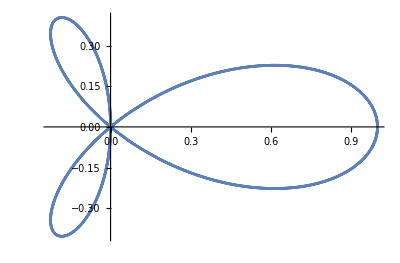
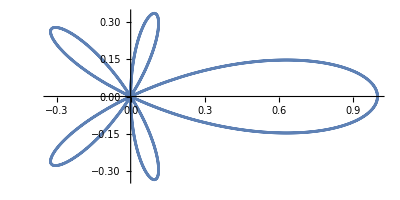
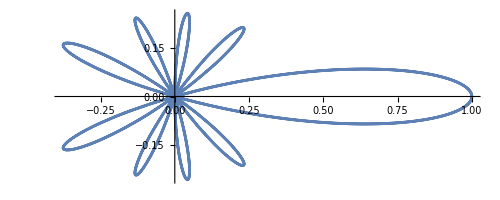
{-Graphics-P_3(cos θ),-Graphics-P_5(cos θ),-Graphics-P_9(cos θ)}

```mathematica
{Labeled[PolarPlot[LegendreP[3,Cos[θ]],{θ,0,2 π}],"P_3(cos θ)",Top],
Labeled[PolarPlot[LegendreP[5,Cos[θ]],{θ,0,2 π}],"P_5(cos θ)",Top],
Labeled[PolarPlot[LegendreP[9,Cos[θ]],{θ,0,2 π}],"P_9(cos θ)",Top]}
```

In most cases, only the first few terms matter—especially P₂—because they capture the most significant shape changes. The higher-order terms do add more detail, but unless the nucleus is really unstable or highly excited, they don’t affect the overall picture much. That’s why this expansion is so useful: it gives us a smooth, mathematical way to track how a nucleus stretches and changes shape, just by tweaking a few parameters. But in practice, we usually focus on just the first two or three terms—P₂ and P₃—because those capture the most physically relevant deformations without over complicating the model. They’re enough to see how a nucleus stretches and becomes unstable, while still keeping the math manageable.

## The 2-D Model

Instead of tracking every particle, we model the radius of the nucleus as a smooth function of angle: Small deviations from a sphere can be described as:

	r(θ) = R[1 + ∑α_n P_n(cosθ)]

R is the average radius
α_n are the deformation ampiltudes (This is only valid when α ≪1 small deviations from spherical shape).
P_n(cosθ) are Legendre polynomials

Let’s define this crucial formula in Mathematica. Here is a 2D model of the LDM using only n of 2 and 4. The orange circle is our model and the blue circle is a constant sphere:

```mathematica
{Animate[Module[{r=1,alpha2=0.5,alpha4=0.15},PolarPlot[{r,r (1+alpha2 LegendreP[2,Cos[θ]]Sin[2Pi t]-alpha4 LegendreP[4,Cos[θ]]Sin[4Pi t])},{θ,0,2Pi},PlotRange->{{-2,2},{-2,2}}]],{t,0,1}]}
```

{}

## A 3-D Model

Now we will jack up the realistic of the model, by making it a three-dimensional drop, using SphericalPlot3D. I used

```mathematica
Animate[Module[{r0=1,α2=0.5,α4=0.3},SphericalPlot3D[r0 (1+α2 LegendreP[2,Cos[θ]]Sin[2 Pi t]+α4 LegendreP[4,Cos[θ]] Sin[4 Pi t]),{θ,0,Pi},{ϕ,0,2 Pi},Boxed->False,Axes->False,Mesh->None]],{t,0,.3}]
```

## The Model Results

As we move from a 3D visualization, we can ask: How do the parameters 𝛼_2 and 𝛼_4 affect the shape of the nucleus? Why do these specific parameters matter, especially when considering nuclear fission?

To figure it out let’s test two 𝛼_2 and 𝛼_4 pairs, keeping one of them at 0: 
α₂    α₄  
0.3   0.0 
0.0   0.3 
0.3.  0.3

```mathematica
{Animate[Module[{r=1,alpha2=0.3,alpha4=0.0},PolarPlot[{r,r (1+alpha2 LegendreP[2,Cos[θ]]Sin[2Pi t]-alpha4 LegendreP[4,Cos[θ]]Sin[4Pi t])},{θ,0,2Pi},PlotRange->{{-2,2},{-2,2}}]],{t,0,1}], Animate[Module[{r=1,alpha2=0.0,alpha4=0.3},PolarPlot[{r,r (1+alpha2 LegendreP[2,Cos[θ]]Sin[2Pi t]-alpha4 LegendreP[4,Cos[θ]]Sin[4Pi t])},{θ,0,2Pi},PlotRange->{{-2,2},{-2,2}}]],{t,0,1}],
Animate[Module[{r=1,alpha2=0.3,alpha4=0.3},PolarPlot[{r,r (1+alpha2 LegendreP[2,Cos[θ]]Sin[2Pi t]-alpha4 LegendreP[4,Cos[θ]]Sin[4Pi t])},{θ,0,2Pi},PlotRange->{{-2,2},{-2,2}}]],{t,0,1}]}//Row
```

If you squeeze a sphere along one axis (say the top and bottom) so that it becomes flattened, that’s an example of a quadrupole shape. Now, imagine you stretch the nucleus even more in a weird way, so that it starts to have more complicated bumps and dents. This is the hexadecapole moment. It tells us about even finer details.

The parameters α₂ and α₄ ​ control different nuclear deformations. α₂ represents the quadrupole mode, which stretches the nucleus into a dumbbell shape.  α₄ represents the hexadecapole mode, creating a four-lobed structure. Together, they model how a nucleus deforms, with α₂ elongating it and α₄ adding complexity, both of which are key in simulating nuclear fission.

Let’s try some more, exploring this combined quadrupole + hexadecapole interaction.
α₂    α₄  
0.3   0.3 
0.6    0.6

```mathematica
{Animate[Module[{r=1,alpha2=0.3,alpha4=0.3},PolarPlot[{r,r (1+alpha2 LegendreP[2,Cos[θ]]Sin[2Pi t ]-alpha4 LegendreP[4,Cos[θ]]Sin[4Pi t])},{θ,0,2Pi},PlotRange->{{-2,2},{-2,2}}]],{t,0,.7,AnimationRepetitions->1}], Animate[Module[{r=1,alpha2=0.6,alpha4=0.6},PolarPlot[{r,r (1+alpha2 LegendreP[2,Cos[θ]]Sin[2Pi t]-alpha4 LegendreP[4,Cos[θ]]Sin[4Pi t])},{θ,0,2Pi},PlotRange->{{-2,2},{-2,2}}]],{t,0,.7,AnimationRepetitions->1}]}//Row
(*This time because of the use of the Sin multiplier we ran the animation to .7 seconds and we ran it only once using AnimationRepetitions*)
```

In the first example, the nucleus is narrowing as it deforms, but has yet to split into 2 fragments. This is option b of Fig 2, or necking which leads to fission. However in the second example, the nucleus is more unstable, and follows similar movements to the first example, but this time it splits. 

These fission parameters describe how this deformation progresses, with critical necking marking the point when the nucleus can no longer hold together.

In fact, after many  α₂ and α₄ combinations, binary fission occurs when the magnitude of the nuclear shape is equal or greater than 0.6. And as shown The magnitude or “deformation” of a nuclear shape is defined below: 

√(𝛼_2^2+ 𝛼_4^2)
​
The reason is that if we consider 𝛼_2 and 𝛼_4 as coordinates for the shape of the nucleus, each point (𝛼_2, 𝛼_4) in the plane corresponds to a particular deformation of the nucleus. By calculating the square root of the sum of their squares, we can find the radial distance from the origin (where 𝛼_2=0 and 𝛼_4=0). The idea here is that nuclear deformation behavior can be characterized by how far the shape is from a “spherical” or stable state. A smaller distance means less deformation (stable), and a larger distance means more deformation (unstable or fission).

By analyzing this model there’s three possibilities: 
1) Stable   – when  √(𝛼_2^2+ 𝛼_4^2) (aka deformation) < 0.3 , the nucleus is stable.
2) Necking  – If 0.3 ≤ deformation < 0.6, the nucleus is nearing fission (splitting).
3) Unstable (fission) – when the deformation ≥ 6, the nucleus is unstable and likely to undergo fission.

Let’s plot that!

I used a CounterPlot where I plotted the deformation with 𝛼_2 and 𝛼_4 range from 0 to 0.8. The pure function plugs in the value of the deformation. The ColorFunction defines a color based on that value. The color of each region is determined by an If statement: light blue for stable regions, orange for necking , and red for unstable regions. Contours just defines where to draw the lines.

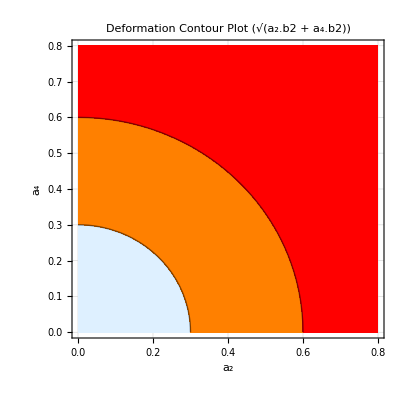

```mathematica
ContourPlot[Sqrt[a2^2+a4^2],{a2,0,0.8},{a4,0,0.8},Contours->{0.3,0.6},ColorFunction->(If[#<0.3,LightBlue,If[#<0.6,Orange,Red]]&),FrameLabel->{"a₂","a₄"},PlotLabel->"Deformation Contour Plot (√(a₂.b2 + a₄.b2))",GridLines->Automatic]
```

## Comparison with Experiment

Next, we’ll dive into a comparison between the theoretical predictions and the experimental results presented in this paper, and see how well the model holds up when applied to actual data from fission experiments.

The paper “Nuclear fission: a review of experimental advances and phenomenology” by A.N. Andreyev is a review of experimental progress in nuclear fission research from the mid-1990s to 2017. You can view the article by putting this link into SciHub: https://iopscience.iop.org/article/10.1088/1361-6633/aa82eb. 


In the paper, it talks about the limits of the liquid drop model. Specifically, according to LDM, most heavy nuclei should break up evenly, creating two fragments of roughly the same mass. But that’s not what really happens. Experiments have shown that fission usually doesn’t split a nucleus evenly. Instead, it often breaks into unequal parts. This review focuses on how scientists discovered that this odd behavior is due to quantum effects that the LDM doesn’t take into account. Specifically, it’s the shell effects (a stability that arises when certain numbers of protons or neutrons are present) that push the system toward breaking unevenly. This is similar to how noble gases are stable because of filled electron shells; certain “magic numbers” of neutrons and protons make nuclei more stable, affecting how they split during fission.

Here is a figure and excerpt of this paper that show the theoretical (LDM only) vs experimental model (LDM and shell interaction) of^238U nucleus. Highlighted sections of the excerpt shows where the limits of the LDM model lies in. 

-Graphics--Graphics-

One of the most important examples discussed is the beta-delayed fission of ^180 Hg, studied at CERN. This experiment found that ^180 Hg fissions asymmetrically, which is completely unexpected according to LDM — it should have split symmetrically. The result sparked a lot of excitement because it showed a new asymmetric fission mode in a region (lead-to-mercury) that hadn’t been explored much before. 

Here is another figure from the same paper. It plots the elements on an axis of proton (y-axis) and neutron (x-axis) number. It then shows the degree of symmetric and asymmetric byproducts from fission. As you can see that the LDM does well in predicting the majority of elements here, however there are outliers in heavy elements or certain isotopes. 
-Graphics-

## Bonus

Here is some cool images from a paper that studies liquid jets. I stumbled across it by accident but found the images really compelling. Again, I’m no physicist. But it’s interesting that there is a degree of asymmetry in liquid jets, and it makes me ask if Bohr’s and Wheeler’s model was not too off. You can find that liquid jets paper here: https://www.irphe.fr/~fragmix/publis/EV2008.pdf

This is a timelapse from 0 to 60 ms of a 5mm water drop falling in a stream of air.

-Graphics-

This is a binary collision of drops (which it seems like they dyed). Which is cool. I’m not sure if there’s a field in fusion that uses a similar idea.  
-Graphics-

This one is funny. It’s mayonnaise pushed out of a nozzle of a radius of 3mm. It too is a time lapse.
-Graphics-